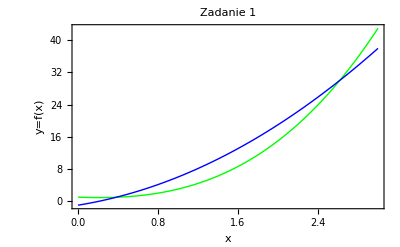

```mathematica
(*Zad 1*)
Clear[x]
f[x_]:=x^3+2x^2-x+1
g[x_]:=f'[x]

Plot[{f[x],g[x]},{x,0,3}, PlotStyle-> {{Green, Thick},{Blue,Thick}},  AxesLabel-> {"x","y=f(x)"}, Frame->True, PlotLabel->"Zadanie 1"]
```

```mathematica
(*Zad 2*)
Program[lista_,n_]:=Module[{wystapienia=0},
For [it = 1,  it≤Length[lista],it++,
If[lista[[it]]==n,wystapienia++];
];
Return [wystapienia];
];
```

```mathematica
list={6,3,2,4,6,2,1,3,4,9,0,2,4,15,23,6,15,12,3,12,512,512,3,123,125,12,51232,123,562,34,268,45,5,345,5234};
```

```mathematica
Program[list,3]
```

4

```mathematica
(*Zad 3*)
Program2[macierz_,n_]:=Module[{iloczyn=1},
If[Length[macierz]<n, Return ["Błąd"]];
For[kol=1,kol≤Length[macierz],kol++,
iloczyn=iloczyn*macierz[[n,kol]];
];
Return[iloczyn];
];
```

```mathematica
mac={{1,2,3},{4,5,6},{7,8,9}};
MatrixForm[mac]
Program2[mac,4]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

Błąd